```mathematica
f[x_]=x^3+1;Lf[z_]=f[z]f''[z]/f'[z]^2; sc[z_]=z-f[z]/f'[z]/(1-Lf[z]);x0=2;
sc[z]//Simplify
x1=N[sc[2]];
grafico1=Plot[{f[x], f[x0]+(f'[x0])^2(x-x0)/(f'[x0]-f''[x0](x-x0)) },{x,-5,2.5}];
```

-(3 z)/(-2+z^3)

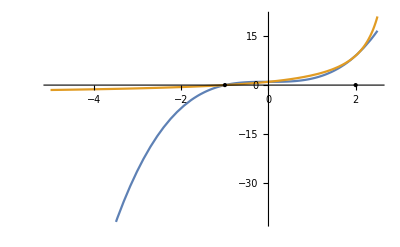

```mathematica
punto0=Graphics[{PointSize[Large],Point[{x0,0}]}];
punto1=Graphics[{PointSize[Large],Point[{x1,0}]}];
Show[{grafico1,punto0,punto1}]
```

```mathematica
x2=N[sc[x1]];
x2
```

-1.

```mathematica
grafico2=Plot[{f[x], f[x1]+(f'[x1])^2(x-x1)/(f'[x1]-f''[x1](x-x1)) },{x,-5,2.5}];
```

```mathematica
punto2=Graphics[{PointSize[Large],Point[{x2,0}]}];
```

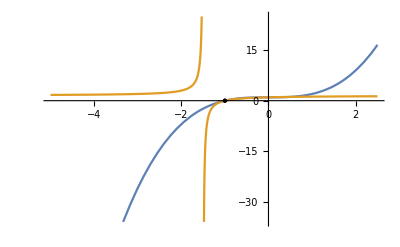

```mathematica
Show[{grafico2,punto2,punto1}]
```